```mathematica
ClearAll["Global`*"]
NotebookDirectory[] ;
SetDirectory[%];
```

```mathematica
r01=0.01;w01=0.0012;alpha1=1.1;alpha2=1;r02=50;
```

```mathematica
zl=0.3;
zs=1;
om=0.3;
h0=67.8;(*km s^-1 Mpc^-1*)
h0c=69.6;(*km s^-1 Mpc^-1*)
c=3*10^5;(*km s^-1*)
(*Mpc=30.85678*10^18 km*)
(*Msun=1.9891*10^30 kg*)
(*G=6.673*10^-11 m^3 kg^-1 s^-2*)
G=6.673*10^-20*1.9891*10^30;(*km^3 Msun^-1 s^-2*)
M=10^10;(*Msun*)
```

```mathematica
H[t_]:=Sqrt[1-om+om *(1+t)^3];
DA[z_]:=c/h0 1/(1+z)NIntegrate[1/H[t],{t,0,z}];
DA2[z1_,z2_]:=c/h0 1/(1+z2)NIntegrate[1/H[t],{t,z1,z2}];
```

```mathematica
thetaE=√((4G*M)/c^2*1/(30.85678*10^18)*DA2[zl,zs]/(DA[zl]*DA[zs]))
b=thetaE*DA[zl]
```

1.13399×10^-6

0.00107642

```mathematica
Sigma0[r_]:=(1+alpha1*((r-r01)/w01)^2)/(1+alpha2*((r-r01)/w01)^2);
```

```mathematica
Sigma[r_]:=Piecewise[{{1,0≤r<r01},{Sigma0[r],r01≤r<=r02},{1,r>r02}}];
```

```mathematica
dSigma0[r_]:=D[Sigma0[a],a]/.a->r
```

```mathematica
dSigma[r_]:=Piecewise[{{0,0≤r<r01},{dSigma0[r],r01<=r≤r02},{0,r>r02}}]
```

```mathematica
PhihMG[L_]:=NIntegrate[-Sigma[r]/r/.r->√(b^2+z^2),{z,0,L}];
```

```mathematica
PhihGR[L_]:=NIntegrate[-1/r/.r->√(b^2+z^2),{z,0,L}];
```

```mathematica
deltaPhi[L_]:=(PhihMG[L]-PhihGR[L])/PhihGR[L];
```

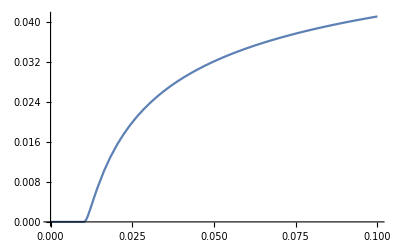

```mathematica
Plot[deltaPhi[L],{L,0,0.1},PlotRange->All]
```

```mathematica
deltaPhidata=Table[{L,deltaPhi[L]},{L,0.001,1,0.001}];
```

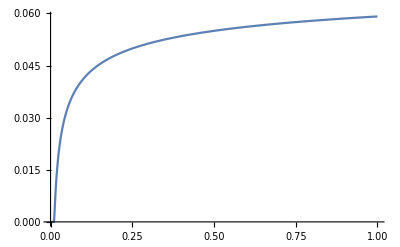

```mathematica
ListLinePlot[deltaPhidata,PlotRange->All]
```

```mathematica
deltaPhidatam=Table[{-deltaPhidata[[n,1]],deltaPhidata[[n,2]]},{n,1,Length[deltaPhidata]}];
```

```mathematica
deltaPhidatat=Sort[Join[deltaPhidata,deltaPhidatam],#1[[1]]<#2[[1]]&];
```

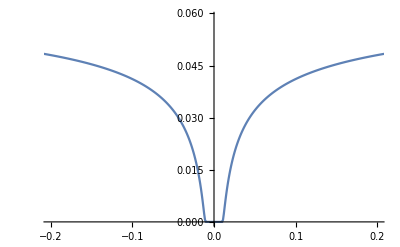

```mathematica
ListLinePlot[deltaPhidatat,PlotRange->{{-0.2,0.2},All}]
```